```mathematica
ClearAll["Global'*"];
$PrePrint = MatrixForm;
```

## Definicje stałych i funkcji

```mathematica
(*Definicje stałych i funkcji*)
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y )
rho0y[y_]:=(rho0 +delRho[y])
delRho[y_]:= (0.1 Sin[2Pi y / (2 ymax)] ) (*Zaburzenie gęstości*)
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])
xi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=(1+H t- 2 Pi G rho0 t^2)   (*czynnik skali dla rho0y = const*)
xiDy[y_,t_]:=(1+H t-2Pi G rho0y[y] t^2) (*pochodna xi po y*)
xiDt[y_,t_]:=(v0[y]-4Pi G m[y]t) (*pochodna xi po t*)

(*Czas po którym warstwa y przekroczyła x=0*)
tCollapse[y_]:=(If[y≥0,tCollapseP[y],tCollapseM[y]]) (*Wolne, jeśli wiadomo znany jest znak y lepiej używać tCollapseM/P*)
tCollapseM[y_]:=(v0[y] - Sqrt[v0[y]^2+8 Pi G m[y]y])/(4 Pi G m[y]) (*dla y < 0*)
tCollapseP[y_]:=(v0[y] +Sqrt[v0[y]^2+8 Pi G m[y]y])/(4 Pi G m[y]) (*dla y > 0*)
tMerge[y_]:=((H + Sqrt[H^2+8 Pi G rho0y[y]])/(4 Pi G rho0y[y]) ) (*Czas rozpoczącia sklejania*)


(*Transformata gęstości po przeskalowaniu x -> x/a[t]*)
rhoScaledkt[k_,t_]:=(NIntegrate[rho0y[y] Exp[-I k / a[t]   xi[y,t] 2Pi/(2ymax)],{y,-ymax,ymax}])

(*Transformata prędkości po przeskalowaniu x -> x/a[t]*)
vScaledkt[k_,t_]:=(NIntegrate[xiDt[y,t]Exp[-I k  xi[y,t]/a[t] 2Pi /(2 ymax)]xiDy[y,t],{y,-ymax,ymax}])

(*Gęstość po przeskalowaniu x -> x/a[t]*)
rhoScaledtx[x_,t_]:=(rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1))

(*Gęstość pędu po przeskalowaniu x -> x/a[t]*)
momentumDensityScaled[x_,t_]:=(rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1) xiDt[(x/a[t]),t])
```

## Charakterystyczne wielkości

```mathematica
(*Czas po którym wszystkie warstwy przekroczyły zero*)
tmax=Max[NMaximize[{tCollapseM[y],-ymax≤ y < 0},y][[1]],NMaximize[{tCollapseP[y],0< y ≤ ymax},y][[1]]]
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}]; (*Czas po którym wszystkie warstwy zaczynają zawracać*)
ta0=t/.Solve[{a[t]==0, 0≤t≤tmax},t][[1]]; (*Czas dla którego a[t]==0 *)
(*If[ta0==t/.{}⟦1⟧,{ta0=tbounce;Print["a[t]!=0"]},Null];*)
amax=FindMaximum[a[t],{t,tmax/2}][[1]]; (*Maksymalne a[t]*)
Print["tmax: ",tmax, ", tbounce ",tbounce,", t[a=0] ",ta0,", amax ",amax]
```

18.1065

tmax: 18.1065, tbounce 8.4988, t[a=0] 16.8595, amax 4.97887

## Numeryczna transformata gęstości i jej wykresy

```mathematica
tstep=.1;
ts=Table[t,{t,0,tmax,tstep}];
k=1;
rhoScaledktTab=rhoScaledkt[k,ts];
vkScaledTab=vScaledkt[k,ts];
(*Może rzucać dużo błędów, głównie jeśli całki są bliskie 0 np dla złego modu*)
```

```mathematica
(*Wykresy 1 modu przeskalowanej transformaty gęstości*) (*Czerwona linia: tbounce*)
plotrhoRe=ListLinePlot[Thread[{ts,Re[rhoScaledktTab]}],PlotLabels->{"Re"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
plotrhoIm=ListLinePlot[Thread[{ts,Im[rhoScaledktTab]}],PlotLabels->{"Im"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
plotrhoMod=ListLinePlot[Thread[{ts,Abs[rhoScaledktTab]^2}],PlotLabels->{"| |^2"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

## Różne wykresy

```mathematica
(*Wykres xi*)
Plot3D[xi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

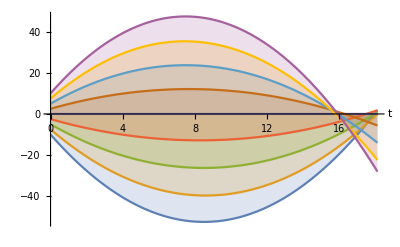

```mathematica
(*Trajektorie*)
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax},AxesLabel->Automatic,Filling->Axis]
```

```mathematica
(*wykres przeskalowanej gęstości*)
Plot3D[rhoScaledtx[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Wykres przeskalowanej gęstości pędu [x/a[t]]*)
Plot3D[momentumDensityScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-

## Rozwiązanie równań pierwszego rzedu zaburzeń

```mathematica
(*Rozwiązanie równania na pierwszy rząd zaburzeń + wykresy*)
dv0= 0;
drho0=rhoScaledktTab[[1]];
solv=NDSolve[{dv''[t]==4 Pi G rho0/a[t] dv[t],dv'[0]== I 4 Pi G /k(drho0),dv[0]==dv0},{dv[t],dv'[t]},{t,0,tmax} ];

plotvSolutionRe=Plot[Evaluate[{Re[dv[t]]}/.solv],{t,0,ta0},AxesLabel->Automatic];
plotvSolutionIm=Plot[Evaluate[{Im[dv[t]]}/.solv],{t,0,ta0},AxesLabel->Automatic];
plotrhoSolutionRe=Plot[Evaluate[{Re[dv'[t]I k/( -4 Pi G)]}/.solv],{t,0,ta0},AxesLabel->Automatic,PlotStyle->Orange];
plotrhoSolutionIm=Plot[Evaluate[{Im[dv'[t]I k/( -4 Pi G)]}/.solv],{t,0,ta0},AxesLabel->Automatic,PlotStyle->Orange];
plotrhoSolutionMod=Plot[Evaluate[{Abs[dv'[t]I k/( -4 Pi G)]^2}/.solv],{t,0,ta0},AxesLabel->Automatic,PlotStyle->Orange];
```

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Show[plotrhoRe,plotrhoSolutionRe,PlotRange->All]
Show[plotrhoIm,plotrhoSolutionIm, PlotRange->All]
Show[plotrhoMod,plotrhoSolutionMod, PlotRange->All]
```

## Różnica między numerycznymi i analitycznymi wynikami

```mathematica
(*Różnica między transformatą gęstości liczona numerycznie i analitycznie z 1. rzedu zaburzeń dla t = 10 w zależności od amplitudy zaburzenia*)
rhoDifference[amp_]:=(
delRho[y_]:=amp Sin[(2 π y)/(2 ymax)];
tmax=Max[NMaximize[{tCollapseM[y],-ymax≤ y < 0},y][[1]],NMaximize[{tCollapseP[y],0< y ≤ ymax},y][[1]]];
ts=Table[t,{t,0,tmax,tstep}];
rhokScaled1=rhoScaledkt[k,ts];
drho0=rhokScaled1[[1]];
dv0=0;
solv=NDSolve[{dv''[t]==4 Pi G rho0/a[t] dv[t],dv'[0]== I 4 Pi G /k(drho0),dv[0]==dv0},{dv[t],dv'[t]},{t,0,ta0} ];
(Abs[dv'[t]I k/( -4 Pi G)]^2/.solv/.t->10)-Abs[rhokScaled1[[101]]]^2)
```

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

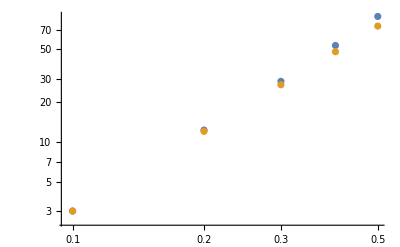

```mathematica
amps={};
diffs={};
For[amp=0.1,amp≤ 0.5, amp+=0.1, AppendTo[amps,amp];AppendTo[diffs,rhoDifference[amp][[1]]]]
ListLogLogPlot[{Thread[{amps,diffs}],Table[{x,300x^2},{x,0.1,.5,0.1}]}]
```

## Badanie zachowania peaku transformaty gęstości

```mathematica
(*Funkcja robiąca wykresy i znajdująca wysokość i położenie peaków dla zaburzenia gęstości o amplitudach a1 i a2 oraz modach k1 i k2:
delRho1 = a1 Sin[2 Pi k1 y / (2 ymax)]
delRho2 = delRho1+ a2 Sin[2 Pi k2 y / (2 ymax)]*)
makePlots[a1_,a2_,k1_,k2_]:=
(
tstep=.1;
delRho[y_]:=(a1 Sin[2k1 Pi y / (2 ymax)] );
tmax1=tmax=Max[NMaximize[{tCollapseM[y],-ymax≤ y < 0},y][[1]],NMaximize[{tCollapseP[y],0< y ≤ ymax},y][[1]]];
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}];
ts1=Table[t,{t,0,tmax1,tstep}];
rhokScaledTab1=rhoScaledkt[k1,ts1];
plotrho1Re=ListLinePlot[Thread[{ts1,Re[rhokScaledTab1]}],PlotLabels->{"Re, 1"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Green}},None},PlotRange->All,PlotStyle->{Black}];
plotrho1Im=ListLinePlot[Thread[{ts1,Im[rhokScaledTab1]}],PlotLabels->{"Im, 1"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Green}},None},PlotRange->All,PlotStyle->{Black}];
plotrho1Mod=ListLinePlot[Thread[{ts1,Abs[rhokScaledTab1]^2}],PlotLabels->{"| |^2, 1"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Green}},None},PlotRange->All,PlotStyle->{Black}];

drho0=rhokScaledTab1[[1]];
dv0=0;
solv=NDSolve[{dv''[t]==4 Pi G rho0/a[t] dv[t],dv'[0]== I 4 Pi G /k(drho0),dv[0]==dv0},{dv[t],dv'[t]},{t,0,tmax1} ];
plotrhoSolutionRe=Plot[Evaluate[{Re[dv'[t]I k/( -4 Pi G)]}/.solv],{t,0,tmax1},AxesLabel->Automatic,PlotStyle->{Orange},PlotLabels->{"Re, sol"}];
plotrhoSolutionIm=Plot[Evaluate[{Im[dv'[t]I k/( -4 Pi G)]}/.solv],{t,0,tmax1},AxesLabel->Automatic,PlotStyle->{Orange},PlotLabels->{"Im, sol"}];
plotrhoSolutionMod=Plot[Evaluate[{Abs[dv'[t]I k/( -4 Pi G)]^2}/.solv],{t,0,tmax1},AxesLabel->Automatic,PlotStyle->{Orange},PlotLabels->{"| |^2, sol"},PlotRange->{0,Max[Abs[rhokScaled1]^2]}];

delRho[y_]:=(a1 Sin[2k1 Pi y / (2 ymax)] + a2 Sin[2k2 Pi y / (2 ymax)]);
tmax2=tmax=Max[NMaximize[{tCollapseM[y],-ymax≤ y < 0},y][[1]],NMaximize[{tCollapseP[y],0< y ≤ ymax},y][[1]]];
Print["tmax1 ",tmax1," tmax2 ",tmax2];
ts2=Table[t,{t,0,tmax2,tstep}];
rhokScaledTab2=rhoScaledkt[k1,ts2];
plotrho21Re=ListLinePlot[Thread[{ts2,Re[rhokScaledTab2]}],PlotLabels->{"Re, 2"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},PlotRange->All];
plotrho2Im=ListLinePlot[Thread[{ts2,Im[rhokScaledTab2]}],PlotLabels->{"Im, 2"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},PlotRange->All];
plotrho2Mod=ListLinePlot[Thread[{ts2,Abs[rhokScaledTab2]^2}],PlotLabels->{"| |^2, 2"},AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},PlotRange->All];

s1=Show[plotrho1Mod,plotrhoSolutionMod,plotrho2Mod,ImageSize->Large,PlotRangePadding->Scaled[.05],PlotLabel->Row@{"a1 = ",a1,", a2 = ",a2,", k1 = ",k1,", k2 = ",k2}];

indexRho1max=Position[Abs[rhokScaledTab1]^2,Max[Abs[rhokScaledTab1]]^2][[1]][[1]];
indexRho2max=Position[Abs[rhokScaledTab2]^2,Max[Abs[rhokScaledTab2]]^2][[1]][[1]];
ts1max=ts1[[indexRho1max]];
ts2max=ts1[[indexRho2max]];
rhok1max=Abs[rhokScaledTab1[[indexRho1max]]]^2;
rhok2max=Abs[rhokScaledTab2[[indexRho2max]]]^2;
Return[{s1,ts1max,rhok1max,ts2max,rhok2max}]
(*Pomarańcza = Solution, 1 Czarny = Mod 1, 2 Blue = Mod 1 + Mod 2*)
)
```

```mathematica
masterTable=Table[makePlots[a1,a2,1,k2],{a1,.1,.5,.1},{a2,.1,.5,.1},{k2,{2,3,4,5,10,20}}]
(*masterTable=Table[makePlots[a1,a2,1,k2],{a1,.1,.5,.5},{a2,.1,.5,.5},{k2,{2}}]*)
(*Instrukcja masterTable:
[[a1]][[a2]][[k2]][[{wykres | |^2, t peaku 1, rho peaku 1, t peaku 2, rho peaku 2}]]*)
```

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 19.2164

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 18.8876

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 18.6927

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 18.5719

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 18.272

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 18.1855

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 20.8283

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 20.4469

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 20.2294

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 20.0951

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 19.8256

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 18.2664

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 22.7876

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 22.3332

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 22.0773

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 21.9194

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 21.6017

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 21.445

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 25.1866

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 24.6318

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 24.3218

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 24.1308

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 23.7465

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 23.5566

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 28.1828

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 18.1065 tmax2 27.4873

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 27.1014

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 26.8641

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 26.3872

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 18.1065 tmax2 26.1518

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 20.6295

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.8899

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 20.0443

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 19.9111

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.7536

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 19.6571

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 22.388

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 21.5046

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 21.0003

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 20.6948

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.9579

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.7511

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 24.6193

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 23.5584

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 22.9715

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 22.6174

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 21.9294

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.8461

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 27.4187

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 26.1099

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 25.3993

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 24.9723

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 24.1426

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 19.9445

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 30.9963

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 29.3313

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 28.4412

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 27.9092

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 19.5643 tmax2 26.8785

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 19.5643 tmax2 20.0563

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 22.3871

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.5427

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.8654

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 21.6491

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.5117

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 21.402

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 24.3172

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 22.7806

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 22.4731

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 22.2077

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.7552

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 21.5143

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 26.8864

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 25.0115

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 23.9947

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 23.3964

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 22.0056

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.6279

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 30.2069

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 27.8595

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 26.627

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 25.9073

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 22.2625

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.7428

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 34.5728

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 31.5281

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 29.9727

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 21.2914 tmax2 29.0725

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 27.3964

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 21.2914 tmax2 21.8589

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 24.5668

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 23.626

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.069

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 23.7496

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 23.6317

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 23.5044

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 26.7263

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.3376

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.8133

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 24.4021

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 23.9267

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 23.641

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 29.7384

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 26.7543

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 25.6071

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 25.138

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.2318

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 23.7793

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 33.7668

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 29.9564

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 28.0367

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 26.9513

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.5458

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 23.9193

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 39.2508

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 34.1841

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 31.7383

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 30.3745

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 23.3702 tmax2 24.8686

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 23.3702 tmax2 24.061

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 27.2966

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.1974

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.7899

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 26.3363

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.2383

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 26.0869

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 29.7849

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.7792

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 27.7227

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 27.1111

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.6032

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 26.2566

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 33.408

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 28.875

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 28.7254

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 28.0118

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.983

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 26.4286

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 38.4463

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 32.5086

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 29.8062

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 29.0037

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 27.3755

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 26.603

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 45.6076

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 37.454

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 33.794

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

tmax1 25.9207 tmax2 31.8406

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 27.7806

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

NMaximize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

tmax1 25.9207 tmax2 26.7798

{{{{-Graphics-,16.,150.532,15.9,122.33},{-Graphics-,16.,150.532,15.8,100.556},{-Graphics-,16.,150.532,16.,136.677},{-Graphics-,16.,150.532,16.,143.248},{-Graphics-,16.,150.532,16.,148.22},{-Graphics-,16.,150.532,16.,149.951}},{{-Graphics-,16.,150.532,15.7,80.0857},{-Graphics-,16.,150.532,15.5,62.9499},{-Graphics-,16.,150.532,15.9,105.787},{-Graphics-,16.,150.532,15.9,120.573},{-Graphics-,16.,150.532,16.,141.442},{-Graphics-,16.,150.532,16.,148.22}},{{-Graphics-,16.,150.532,15.4,52.1482},{-Graphics-,16.,150.532,15.2,41.5989},{-Graphics-,16.,150.532,15.7,76.4063},{-Graphics-,16.,150.532,15.8,94.6429},{-Graphics-,16.,150.532,16.,130.664},{-Graphics-,16.,150.532,16.,145.367}},{{-Graphics-,16.,150.532,15.1,35.9135},{-Graphics-,16.,150.532,16.2,32.0664},{-Graphics-,16.,150.532,15.5,54.9666},{-Graphics-,16.,150.532,15.7,71.9739},{-Graphics-,16.,150.532,15.9,118.703},{-Graphics-,16.,150.532,16.,141.442}},{{-Graphics-,16.,150.532,14.9,26.1731},{-Graphics-,16.,150.532,16.1,32.6015},{-Graphics-,16.,150.532,15.2,40.8688},{-Graphics-,16.,150.532,15.5,55.3973},{-Graphics-,16.,150.532,15.9,105.528},{-Graphics-,16.,150.532,16.,136.513}}},{{{-Graphics-,15.2,167.044,15.2,158.438},{-Graphics-,15.2,167.044,15.1,141.011},{-Graphics-,15.2,167.044,15.2,163.237},{-Graphics-,15.2,167.044,15.2,165.524},{-Graphics-,15.2,167.044,15.2,166.423},{-Graphics-,15.2,167.044,15.2,166.888}},{{-Graphics-,15.2,167.044,15.1,137.284},{-Graphics-,15.2,167.044,14.9,114.324},{-Graphics-,15.2,167.044,15.2,152.207},{-Graphics-,15.2,167.044,15.2,159.167},{-Graphics-,15.2,167.044,15.2,164.573},{-Graphics-,15.2,167.044,15.2,166.423}},{{-Graphics-,15.2,167.044,14.9,113.443},{-Graphics-,15.2,167.044,14.6,91.6832},{-Graphics-,15.2,167.044,15.1,136.896},{-Graphics-,15.2,167.044,15.2,148.392},{-Graphics-,15.2,167.044,15.2,161.523},{-Graphics-,15.2,167.044,15.2,165.65}},{{-Graphics-,15.2,167.044,14.6,92.1618},{-Graphics-,15.2,167.044,14.4,74.0727},{-Graphics-,15.2,167.044,14.9,119.62},{-Graphics-,15.2,167.044,15.1,135.514},{-Graphics-,15.2,167.044,15.2,157.325},{-Graphics-,15.2,167.044,15.2,164.573}},{{-Graphics-,15.2,167.044,14.4,75.2607},{-Graphics-,15.2,167.044,14.1,60.7978},{-Graphics-,15.2,167.044,14.8,103.093},{-Graphics-,15.2,167.044,15.,121.412},{-Graphics-,15.2,167.044,15.2,152.047},{-Graphics-,15.2,167.044,15.2,163.195}}},{{{-Graphics-,14.5,184.84,14.5,180.517},{-Graphics-,14.5,184.84,14.4,166.844},{-Graphics-,14.5,184.84,14.5,182.946},{-Graphics-,14.5,184.84,14.5,184.33},{-Graphics-,14.5,184.84,14.5,184.533},{-Graphics-,14.5,184.84,14.5,184.763}},{{-Graphics-,14.5,184.84,14.4,169.246},{-Graphics-,14.5,184.84,14.2,147.656},{-Graphics-,14.5,184.84,14.4,177.469},{-Graphics-,14.5,184.84,14.5,181.381},{-Graphics-,14.5,184.84,14.5,183.613},{-Graphics-,14.5,184.84,14.5,184.533}},{{-Graphics-,14.5,184.84,14.2,153.502},{-Graphics-,14.5,184.84,14.,129.136},{-Graphics-,14.5,184.84,14.4,169.24},{-Graphics-,14.5,184.84,14.4,176.119},{-Graphics-,14.5,184.84,14.5,182.087},{-Graphics-,14.5,184.84,14.5,184.149}},{{-Graphics-,14.5,184.84,14.1,136.574},{-Graphics-,14.5,184.84,13.8,112.542},{-Graphics-,14.5,184.84,14.3,158.722},{-Graphics-,14.5,184.84,14.4,169.249},{-Graphics-,14.5,184.84,14.5,179.967},{-Graphics-,14.5,184.84,14.5,183.613}},{{-Graphics-,14.5,184.84,13.9,120.274},{-Graphics-,14.5,184.84,13.5,98.3092},{-Graphics-,14.5,184.84,14.2,146.94},{-Graphics-,14.5,184.84,14.3,160.653},{-Graphics-,14.5,184.84,14.4,177.409},{-Graphics-,14.5,184.84,14.5,182.925}}},{{{-Graphics-,13.8,203.79,13.8,201.241},{-Graphics-,13.8,203.79,13.7,189.909},{-Graphics-,13.8,203.79,13.8,202.668},{-Graphics-,13.8,203.79,13.8,203.596},{-Graphics-,13.8,203.79,13.8,203.608},{-Graphics-,13.8,203.79,13.8,203.744}},{{-Graphics-,13.8,203.79,13.7,194.212},{-Graphics-,13.8,203.79,13.5,174.828},{-Graphics-,13.8,203.79,13.8,199.331},{-Graphics-,13.8,203.79,13.8,201.956},{-Graphics-,13.8,203.79,13.8,203.064},{-Graphics-,13.8,203.79,13.8,203.608}},{{-Graphics-,13.8,203.79,13.6,183.653},{-Graphics-,13.8,203.79,13.4,159.658},{-Graphics-,13.8,203.79,13.7,194.201},{-Graphics-,13.8,203.79,13.8,198.894},{-Graphics-,13.8,203.79,13.8,202.16},{-Graphics-,13.8,203.79,13.8,203.381}},{{-Graphics-,13.8,203.79,13.5,171.011},{-Graphics-,13.8,203.79,13.2,145.195},{-Graphics-,13.8,203.79,13.7,187.282},{-Graphics-,13.8,203.79,13.7,194.593},{-Graphics-,13.8,203.79,13.8,200.9},{-Graphics-,13.8,203.79,13.8,203.064}},{{-Graphics-,13.8,203.79,13.3,157.552},{-Graphics-,13.8,203.79,13.,131.85},{-Graphics-,13.8,203.79,13.6,179.191},{-Graphics-,13.8,203.79,13.7,189.25},{-Graphics-,13.8,203.79,13.8,199.287},{-Graphics-,13.8,203.79,13.8,202.657}}},{{{-Graphics-,13.1,223.997,13.1,222.347},{-Graphics-,13.1,223.997,13.,212.545},{-Graphics-,13.1,223.997,13.1,223.264},{-Graphics-,13.1,223.997,13.1,223.918},{-Graphics-,13.1,223.997,13.1,223.878},{-Graphics-,13.1,223.997,13.1,223.967}},{{-Graphics-,13.1,223.997,13.1,217.465},{-Graphics-,13.1,223.997,12.9,200.127},{-Graphics-,13.1,223.997,13.1,221.077},{-Graphics-,13.1,223.997,13.1,222.896},{-Graphics-,13.1,223.997,13.1,223.524},{-Graphics-,13.1,223.997,13.1,223.878}},{{-Graphics-,13.1,223.997,13.,209.967},{-Graphics-,13.1,223.997,12.8,187.276},{-Graphics-,13.1,223.997,13.1,217.469},{-Graphics-,13.1,223.997,13.1,220.938},{-Graphics-,13.1,223.997,13.1,222.934},{-Graphics-,13.1,223.997,13.1,223.731}},{{-Graphics-,13.1,223.997,12.9,200.466},{-Graphics-,13.1,223.997,12.6,174.71},{-Graphics-,13.1,223.997,13.,212.605},{-Graphics-,13.1,223.997,13.1,218.063},{-Graphics-,13.1,223.997,13.1,222.11},{-Graphics-,13.1,223.997,13.1,223.524}},{{-Graphics-,13.1,223.997,12.8,189.727},{-Graphics-,13.1,223.997,12.4,162.615},{-Graphics-,13.1,223.997,13.,206.739},{-Graphics-,13.1,223.997,13.1,214.3},{-Graphics-,13.1,223.997,13.1,221.053},{-Graphics-,13.1,223.997,13.1,223.258}}}}

```mathematica
as=Table[a1,{a1,.1,.5,.1}];
ks=Table[k2,{k2,{2,3,4,5,10,20}}];
ListPlot[Table[{ks[[i]],masterTable[[1]][[1]][[i]][[5]]/masterTable[[1]][[1]][[i]][[3]]},{i,1,6}]]
```

-Graphics-

```mathematica
(*Wykresy a1-a2-czas peaku dla różnych drugich modów*)
For[kI=1,kI≤6,kI+=1,ListPlot3D[Flatten[Table[{as[[a1]],as[[a2]],masterTable[[a1]][[a2]][[kI]][[4]]/masterTable[[a1]][[a2]][[kI]][[2]]},{a1,1,5},{a2,1,5}],1],Mesh->All,AxesLabel->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->Row@{"tmax2/tmax2, k2 = ",ks[[kI]]}]//Print]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
(*Wykresy a1-a2-wielkość peaku dla różnych drugich modów*)For[kI=1,kI≤6,kI+=1,ListPlot3D[Flatten[Table[{as[[a1]],as[[a2]],masterTable[[a1]][[a2]][[kI]][[5]]/masterTable[[a1]][[a2]][[kI]][[3]]},{a1,1,5},{a2,1,5}],1],Mesh->All,AxesLabel->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->Row@{"rhomax2/rhomax1, k2 = ",ks[[kI]]}]//Print]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
(*Ładna faktoryzacja pochodnej czasu przekraczania zera*)
vA[y_]:=h y
rho0yA[y_]:=rho0A+delRhoA[y]
mA[y_]:=(Integrate[rho0yA[yy],{yy,0,y}])
tAP[y_]:=( vA[y]+ Sqrt[vA[y]^2+8 Pi g mA[y]y])/(4 Pi g mA[y])
Simplify[D[tAP[y],{y,1}]]
```

-((rho0A y+y delRhoA[y]-∫_0^y (rho0A+delRhoA[yy])ⅆyy) (4 g π ∫_0^y (rho0A+delRhoA[yy])ⅆyy+h (h y+√(y (h^2 y+8 g π ∫_0^y (rho0A+delRhoA[yy])ⅆyy)))))/(4 g π (∫_0^y (rho0A+delRhoA[yy])ⅆyy)^2 √(y (h^2 y+8 g π ∫_0^y (rho0A+delRhoA[yy])ⅆyy)))

```mathematica
Export["masterTable5_5_6.mx",masterTable]
```

masterTable5_5_6.mx

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/maciej/Studia/CFT_praktyki/sgds

```mathematica
(*Wczytywanie z pliku *) 
masterTable=Import["masterTable5_5_6.mx"];
```